# Multielectron Atoms and Approximate Solutions

## Purpose

The purpose of this lesson is to...

describe the use of atomic units in atomic and molecular calculations.

reveal how the Hartree approximation can be utilized to obtain the approximate energies and eigenfunctions of multielectron systems

discuss the importance of electron spin and the antisymmetric exchange requirement in describing multielectron systems.

describe how term symbols can be used to describe the electron configuration of a multielectron system.

introduce two of the major approximation methods used to approximately solve multi-electron systems: the variational method and perturbation theory.

reveal how we can construct a wavefunction as a linear combination of basis functions and then solve for the weights using a secular determinant.

## Learning Objectives

At the end of this lesson, I should be able to...

use atomic units in setting up the TISE and convert between atomic units and SI units.

apply the variational method and variational principle to find the best approximation of the true wavefunction and energy for a given trial function.

describe the procedure for calculating the approximate ground-state energy and eigenstate of a system through the Hartree-Fock method.

explain the antisymmetric exchange condition and how it is accounted for in the Hartree-Fock method.

describe how a Slater determinant can be used to construct a properly antisymmetrized wavefunction.

apply the variational method and variational principle to find the best approximation of the true wavefunction and energy for a given trial function.

set up a secular determinant to solve for the approximate energies and wavefunctions of a system.

## Notes About Atomic Units

### What Are Atomic Units?

Up to this point in the class, we have stuck pretty consistently with the use of SI units for all of our calculations, demonstrations, and exercises. However, we’ve seen that sometimes these units leave us with many, many constants in our answers. For example, we saw that the ground-state energy of the hydrogen atom is written

E_(H_(1s))=-(m_e e^4)/(32 π^2 ϵ_0 ℏ^2)

But we have already seen that many of our answers in the case of atoms have been yielding multiples of a certain values. In fact, we’ve already been using the Bohr radius, a_0, as a means to simplify our input and output when discussing the radial dependence of hydrogen atomic wavefunctions.

Atomic units are simply a set of such collections of constants that simplify our equations and our answers when working with calculations of atoms and molecules. For example, the atomic unit of energy is the Hartree, E_h,

E_h=(m_e e^4)/(16 π^2 ϵ_0 ℏ^2)

Using this unit, we see that the ground-state energy of the hydrogen atom is just −E_h/2, or −0.5 Hartrees. A list of such units is given in the table below. Essentially all software for performing computational chemistry utilizes atomic units in its output.

```mathematica
headings={"Property", "Atomic Unit", "Value in SI Units"};
data={
{"mass","mass of electron, m_e", "9.1094 × 10^(−31) kg"}
,
{"charge","magnitude of electron charge, e", "1.6022 × 10^(−19) C"}
,
{"angular momentum","reduced Planck's constant, ℏ", "1.0546 × 10^(−34) J s"}
,
{"distance","Bohr radius, a_0", "5.2918 × 10^(−11) m"}
,
{"energy","Hartree, E_h=(m_e e^4)/(16 π^2 ϵ_0 ℏ^2)", "4.3597 × 10^(−18) J"}
,
{"permittivity","4πϵ_0", "1.1127 × 10^(−10) C^2 J^(−1) m^(−1)"}
};
gridfill=Prepend[data,headings];
Grid[gridfill,BaseStyle->{FontFamily->"SourceSerifPro",FontSize->20},ItemStyle->{Automatic,{1->{Bold,14}}},Frame->{All,1->True}]
```

Property | Atomic Unit | Value in SI Units
mass | mass of electron, m_e | 9.1094 × 10^(−31) kg
charge | magnitude of electron charge, e | 1.6022 × 10^(−19) C
angular momentum | reduced Planck's constant, ℏ | 1.0546 × 10^(−34) J s
distance | Bohr radius, a_0 | 5.2918 × 10^(−11) m
energy | Hartree, E_h=(m_e e^4)/(16 π^2 ϵ_0 ℏ^2) | 4.3597 × 10^(−18) J
permittivity | 4πϵ_0 | 1.1127 × 10^(−10) C^2 J^(−1) m^(−1)

### Why Use Atomic Units?

Atomic units can be a bit annoying if you are used to working in SI units, but they do have some utility. Unfortunately, once one moves away from the hydrogen atom, most calculations don’t return nice multiple values of atomic units. However, they do greatly simplify the form in which we write equations. Take, for example, our TISE for the helium atom,

-ℏ^2/(2 m_e)(∇_1^2 +∇_2^2)ψ(r_1, r_2)-(2 e^2)/(4 πϵ_0)(1/r_1+1/r_2)ψ(r_1,r_2)+e^2/(4 πϵ_0|r_1-r_2|)ψ(r_1,r_2)=Eψ(r_1,r_2)

If we write down this same equation in atomic units instead of SI units, we obtain

-1/2(∇_1^2 +∇_2^2)ψ(r_1, r_2)-2(1/r_1+1/r_2)ψ(r_1,r_2)+1/(|r_1-r_2|)ψ(r_1,r_2)=Eψ(r_1,r_2)

So you can see that in this form, our TISE doesn’t have quite so many constants floating about. Another important advantage (that may not effect your day-to-day use) is that the units are independent of the value of any constants. So, if the value of a constant changes, it doesn’t change the value in atomic units, only the value of its conversion to SI units. In any case, atomic units are a standard in computational chemistry, so you have to get used to using them and converting between SI and atomic units.

## Finding the Energies and Eigenstates of Multielectron Atoms

### The Challenge of Multielectron Systems

As discussed at the end of the lesson on the hydrogen atom, we immediately encounter problems in solving the Hamiltonian for even a two-electron system. We usually start with the approximation that the nucleus is in a fixed position and solve the time-independent Schrödinger equation for electron position relative to the nucleus. This approximation is valid because the mass of the nucleus is much greater than the mass of the electrons (M>>m_e), meaning the center of mass is roughly located at the center of the atom. Using this simplification, we can write the time-independent Schrödinger equation for the helium atom (2 electrons) as

-ℏ^2/(2 m_e)(∇_1^2 +∇_2^2)ψ(r_1, r_2)-(2 e^2)/(4 πϵ_0)(1/r_1+1/r_2)ψ(r_1,r_2)+e^2/(4 πϵ_0|r_1-r_2|)ψ(r_1,r_2)=Eψ(r_1,r_2)

where the 1 and 2 designations refer to electrons 1 and 2.

Unfortunately, we cannot solve the time-independent Schrödinger equation of the helium atom because of the interelectronic repulsion term in the Hamiltonian,

1/(|r_1-r_2|)=1/r_12

which depends simultaneously on the positions of electrons 1 and 2, making a separation of variables approach impossible. This term only becomes more problematic as we add more and more electrons. In general, we can write the Hamiltonian for an atom with N electrons and atomic number Z as

Ĥ=-ℏ^2/(2 m_e)(∑_(i=1))^N∇_i^2 -Ze^2/(4 πϵ_0)(∑_(i=1))^N 1/r_i+e^2/(4 πϵ_0)(∑_(j≠i))^N 1/r_ij

or in atomic units,

Ĥ=-1/2(∑_(i=1))^N∇_i^2 -Z(∑_(i=1))^N 1/r_i+(∑_(j≠i))^N 1/r_ij

The first term gives the kinetic energy operator for each electron, the second term gives the attractive potential between the nucleus and each electron, and the third term gives the interelectronic repulsion between each pair of electrons. Note that the final sum is over both j and i (when j ≠ i ).

In short, we need a different strategy to identify the wavefunctions of a multielectron atom. We will use approximations that allow us to identify the form of solutions in these systems.

### Introduction to the Variational Method

The variational method represents a relatively simple yet highly effective approach to solve for the approximate energies and eigenstates of a system that cannot be solved analytically.

Let’s say we have a system that is described by the time-independent Schrödinger equation,

Ĥ|ψ⟩=E|ψ⟩                                           Ĥ ψ=Eψ

where we are now presenting the equation in both bra-ket and traditional forms. We are interested in finding the ground-state energy E_0 and wavefunction ψ_0,

Ĥ|ψ_0⟩=E_0|ψ_0⟩                                      Ĥ ψ_0=E_0 ψ_0

but we cannot solve the TISE analytically. First, let’s obtain an expression for the energy by multiplying both sides of equation (10) by the complex conjugate of the ground-state wavefunction ψ_0^⋆ and integrating over all space,

E_0=⟨ψ_0|Ĥ|ψ_0⟩/⟨ψ_0|ψ_0⟩                                     E_0=(∫ψ_0^⋆ Ĥ ψ_0 dτ)/(∫ψ_0^⋆ψ_0 dτ)

where dτ is the volume element in whatever coordinates we might be working in. As we said, we cannot solve equations (10) or (11) analytically, but let’s say we have a trial solution for ψ_0 that we will call ϕ. We can always represent our trial wavefunction as a linear combination of the true eigenstate wavefunctions ψ_n,

|ϕ⟩=∑_n c_n|ψ_n⟩                                       ϕ=∑_n c_n ψ_n

which have true energy eigenvalues of

Ĥ|ψ_n⟩=E_n|ψ_n⟩                                         Ĥ ψ_n=E_n ψ_n

Remember that all of the true eigenstate wavefunctions are orthonormal, meaning

⟨ψ_m|ψ_n⟩=δ_mn                     ∫ψ_m^⋆ψ_n dτ=δ_mn

Also note that, in accordance with our typical nomenclature,

E_0<E_1<E_2<...

Now, if we replace ψ_0 in equation (11) with our trial wavefunction ϕ, we obtain

E_ϕ=⟨ϕ|Ĥ|ϕ⟩/⟨ϕ|ϕ⟩                                           E_ϕ=(∫ϕ^⋆ Ĥ ϕ dτ)/(∫ϕ^⋆ϕ dτ)

For the numerator, substitution of the definition of ϕ in terms of ψ_n yields

⟨ϕ|Ĥ|ϕ⟩=⟨∑_n c_n ψ_n |Ĥ|∑_m c_m ψ_m ⟩                           ∫ϕ^⋆ Ĥ ϕ dτ=∫∑_n c_n^⋆ψ_n^⋆ Ĥ∑_m c_m ψ_m dτ

=∑_n ∑_m c_n^⋆c_m⟨ψ_n |Ĥ|ψ_m ⟩                                               =∑_n ∑_m c_n^⋆c_m∫ψ_n^⋆ Ĥ ψ_m dτ

=∑_n ∑_m c_n^⋆c_m E_m⟨ψ_n |ψ_m ⟩                                                 =∑_n ∑_m c_n^⋆c_m E_m∫ψ_n^⋆ ψ_m dτ

Applying the orthogonality condition, we obtain

⟨ϕ|Ĥ|ϕ⟩=∑_n c_n^⋆c_n E_n                                                      ∫ϕ^⋆ Ĥ ϕ dτ=∑_n c_n^⋆c_n E_n

Similarly, for the denominator we obtain

⟨ϕ|ϕ⟩=⟨∑_n c_n ψ_n |∑_m c_m ψ_m ⟩                                       ∫ϕ^⋆ ϕ dτ=∫∑_n c_n^⋆ψ_n^⋆ ∑_m c_m ψ_m dτ

=∑_n ∑_m c_n^⋆c_m⟨ψ_n |ψ_m ⟩                                                   =∑_n ∑_m c_n^⋆c_m∫ψ_n^⋆ ψ_m dτ

=∑_n c_n^⋆c_n                                                                             =∑_n ∑_m c_n^⋆c_n

So equation (16) becomes

E_ϕ=(∑_n c_n^⋆c_n E_n)/(∑_n c_n^⋆c_n)

If we subtract from both sides the true ground-state energy E_0, we obtain

E_ϕ-E_0=(∑_n c_n^⋆c_n(E_n -E_0))/(∑_n c_n^⋆c_n)

Because all of the quantities on the right-hand side are positive (remember that the E_n values are simply the energy eigenvalues of higher-energy eigenstates), we come to the conclusion that

E_ϕ≥E_0

which is known as the variational principle. In other words, the energy we obtain from solving the Hamiltonian of our trial wavefunction will always be greater than or equal to the energy of the true wavefunction. That means, for a given trial wavefunction that is a function of some parameters,

ϕ(α,β,γ,...)

the value of the parameters that gives the lowest value of E_ϕ will give the best approximation of the true energy eigenvalues and wavefunction eigenstates.

Thus, the variational method involves selecting a trial wavefunction and adjusting parameters to achieve the lowest-possible energy in the TISE. The ultimate accuracy of the method will depend on how well the trial wavefunction approximates the true wavefunction.

### The Hartree Approximation

The variational method allows us to provide a guess wavefunction and then optimize parameters to find the best possible solution. However, we still need to address what that guess wavefunction might actually look like. Specifically, we have to develop a method to address the challenges of the interelectronic repulsion term, which prevents an exact solution to the TISE. But what if we assume that we can approximate the true wavefunction of the ground states as the product of two hydrogen-like wavefunctions,

ψ(r_1, r_2)≈Φ(r_1, r_2)=ϕ(r_1)ϕ(r_2)

This approach represents the starting point of the Hartree approximation, which assumes that the exact wavefunction of a multielectron system can be approximated as the product of single-electron wavefunctions.

The next step in the Hartree method involves the formulation of an effective potential experienced by an electron due to the other electrons. Let’s continue with the example of the helium atom, which only has two electrons. We have thus far been interpreting the quantity

ϕ^⋆(r_2)ϕ(r_2)ⅆ r_2

as the probability of finding electron 2 in the infinitesimally small volume element ⅆ r_2 located at position r_2. However, we could also think about this quantity as representing the charge density at position r_2. In this case, we can define an effective potential experienced by electron 1 due to the charge density of electron 2 as

V_1^eff(r_1)=∫ϕ^⋆(r_2)e^2/(4 πϵ_0)1/r_12 ϕ(r_2)ⅆ r_2

Once we have the effective potential for electron 1, we can also write the corresponding effective Hamiltonian for electron 1,

(Ĥ)_1^eff=-ℏ^2/(2 m_e)∇_1^2 -(2 e^2)/(4 πϵ_0)1/r_1+V_1^eff(r_1)

We can then solve the time-independent Schrödinger equation of (Ĥ)_1^eff to obtain an approximate energy contribution from electron 1,

(Ĥ)_1^eff ϕ(r_1)=ϵ_1 ϕ(r_1)

Now, if we skip a little bit ahead, we know that there will be two electrons in the 1s orbital of helium as dictated by the Pauli exclusion principle. Because the energetic contribution from each of these electrons will be identical, we only need to solve this equation once to find both ϵ_1 and ϵ_2. We’ll come back to the Pauli exclusion principle and spin in a moment.

### The Self-Consistent Field Method

But how do we even solve the time-independent Schrödinger equation of our effective Hamiltonian? After all, we can see that the answer depends on ϕ(r_2) because V_1^eff depends on r_2. Since we said that ϕ(r_1) and ϕ(r_2) should be the same for the helium atom, it seems we have a cyclic problem where we don’t know the value of  (Ĥ)_1^eff ϕ(r_1)=ϵ_1 ϕ(r_1) unless we already know the value of ϕ(r_1), which we can’t find unless we solve (Ĥ)_1^eff ϕ(r_1)=ϵ_1 ϕ(r_1).

The method to solve such an equation is known as the self-consistent field method. It can be summarized as follows:

Guess a form of ϕ(r_2)and then calculate V_1^eff(r_1)

Solve the TISE of the effective Hamiltonian, (Ĥ)_1^eff ϕ(r_1)=ϵ_1 ϕ(r_1).

Solving the TISE yields a new value for ϕ(r_1). If this differs from the previous guess for ϕ(r_2), change ϕ(r_2)to the new value and run the process again (remember that ϕ(r_1)=ϕ(r_2)).

Keep going until the output function ϕ(r_1) is equal to the input function ϕ(r_2)(or only different by a very small number). In this case, we say that the SCF has converged, and the calculation is completed.

This approach can in general be extended to atoms with even more electrons or even molecules. Essentially all computational chemistry calculations begin with solving a Hamiltonian through a self-consistent field method.

There is a limit to the accuracy of the Hartree method (and the Hartree-Fock method, which we will come to in a moment). Because the method assumes that each electron experiences only the average potential created by the other electrons, any correlation between the electrons is not accounted for in the method. Therefore, we can call the difference between the true energy and the Hartree energy the correlation energy of the system. For helium, the correlation energy (which also tells you about the accuracy of the method) is

CE=E_exact-E_Hartree

CE=-2.9037 Hartrees +2.8617 Hartrees = -0.0420 Hartrees = -110 kJ mol^-1

So the Hartree method overestimates the energy of the system by 110 kJ mol^-1, which is on the order of the strength of a covalent bond. We will see, however, that although the absolute accuracy of the method is not very high, the Hartree-Fock method in particular can give decent approximations if we are only concerned with relative energies that don’t involve bond breaking (because the correlation energy won’t change very much in that case).

To discuss systems with more than two atoms, we must also account for electron spin explicitly, which will lead us to the Hartree-Fock method.

## Electron Spin Angular Momentum

### Electron Spin and the Schrödinger Equation

We are familiar with the concept of electron spin from introductory chemistry courses, but thus far in the course we have only referred to electron spin in passing. That’s because the Schrödinger equation doesn’t account for spin. This problem was discovered relatively early in the history of quantum mechanics.

Stern and Gerlach observed electron spin experimentally in 1922, although they misinterpreted the result at the time. Uhlenbeck and Goudsmit originally proposed in 1925 that the z-component of the spin angular momentum of the electron is quantized in values of ±ℏ/2. We now recognize this quantization of the z-component of spin angular momentum to be specified by a fourth quantum number, typically denoted as m_s, which can take on values of ±1/2.

Because the time-independent Schrödinger equation doesn’t account for spin directly, spin is usually accounted for in an ad hoc manner. In other words, we construct our solutions to the Schrödinger equation in a way that accounts for spin. Spin isn’t derived “naturally” in this approach, but it allows us to continue using the same framework and principles we have developed up to this point.

### Spin Operators, Eigenvalues, and Eigenfunctions

If in fact we have some allowed values for the z-component of the electron spin given by ±ℏ/2, there should be some corresponding spin operator (Ŝ)_z that has eigenvalues ±ℏ/2,

(Ŝ)_z f=m_s ℏf

where

m_s=±1/2

Because there are two eigenvalues for the operator (Ŝ)_z, there are two corresponding eigenfunctions f. Traditionally, these two eigenfunctions are labeled α and β,

(Ŝ)_z α=ℏ/2 α

(Ŝ)_z β=-ℏ/2β

In analogy with the square total angular momentum operator (L̂)^2, we also define a square total spin angular momentum operator (Ŝ)^2,

OverHat[S^2]α=s(s+1)ℏ^2 α

OverHat[S^2]β=s(s+1)ℏ^2 β

In analogy with (L̂)^2 and (L̂)_z, m_s can take on integer values from −s to s. Because we only have two possible values of m_s, we must have only one possible value of s,

s=1/2

Equations (37) and (38) tell us that if we somehow make a measurement of the z-component of the angular momentum of a free electron, we will only obtain values of either ℏ/2 or −ℏ/2 as a result. As a note, we often refer to this spin angular momentum as an intrinsic angular momentum, because it is not associated with a true spinning state of the electron. Note that the eigenvalues S_z and S^2 associated with these operators are given by

S_z=m_s ℏ=±ℏ/2

and

S^2=s(s+1)ℏ^2=1/2(1/2+1)ℏ^2

Because α and β are eigenfunctions of a Hermitian operator, they must be orthogonal. In integral form, we usually write these as a function of some variable σ. Additionally, we take α and β to be normalized, so we have

∫α^⋆(σ)α(σ)ⅆσ=∫β^⋆(σ)β(σ)ⅆσ=1

∫α^⋆(σ)β(σ)ⅆσ=∫β^⋆(σ)α(σ)ⅆσ=0

## Spin, Antisymmetric Exchange, and the Pauli Exclusion Principle

### Wavefunctions and Spin

We stated in our postulates of quantum mechanics that the wavefunction ψ should contain all of the information we can know about a system. Although it is not explicitly accounted for in the Schrödinger equation, we now see that we must include spin in our wavefunction ψ. In the context of multielectron atoms or molecules, we usually take spin into account by writing our one-electron functions (“orbitals”) as a product of spatial and spin components,

χ(r,σ)=ϕ(r)α(σ)

or

χ(r,σ)=ϕ(r)β(σ)

Note that for any spatial orbital ϕ(r), we can have two possible spin components, α or β.

### Particle Labels and the Wavefunction

In the last section, we stated that the wavefunction tells us all of the information we can know about a system. However, the wavefunction should also be consistent with things that we can’t know about a system. Quantum mechanics does not give us any way to differentiate one electron from another (or any one particle from another one), so if we switch the labels we assign to our particles, it shouldn’t change the result we would obtain from any experiment. If we have an electron in an atom that we call electron 3, and we suddenly start calling it electron 1, it makes sense that such a switch in labels shouldn’t change any observables.

Remember that the first postulate of quantum mechanics tells us that the real information we get from a wavefunction comes from its absolute square, with the probability that an object in the state specified by ψ(r, t ) will be found in the volume element dτ located at r at time t  given by

ψ^⋆(r,t)ψ(r,t)dτ

This definition indicates that when we switch the labels of our particles (usually electrons in our case), the absolute square of the wavefunction should not change,

|ψ(r_1,r_2,r_3,...,r_n)|^2=|ψ(r_2,r_1,r_3,...,r_n)|^2

which means that when we switch any labels in our wavefunction, the wavefunction can only change by a factor of ⅇ^ⅈϕ, where ϕ is a phase factor. This requirement can be most easily illustrated for the case where there are two particles, as in helium with two electrons. We then have

|ψ(r_1,r_2)|^2=|ⅇ^ⅈϕ ψ(r_2,r_1)|^2

=(ⅇ^ⅈϕ ψ(r_2,r_1))^⋆(ⅇ^ⅈϕ ψ(r_2,r_1))

=ⅇ^-ⅈϕ ψ^⋆(r_2,r_1)ⅇ^ⅈϕ ψ(r_2,r_1)

=ψ^⋆(r_2,r_1)ψ(r_2,r_1)

=|ψ(r_2,r_1)|^2

Now, we find that if we change the labels again, we must have

|ⅇ^ⅈϕ ψ(r_2,r_1)|^2=|ⅇ^ⅈϕ ⅇ^ⅈϕ ψ(r_1,r_2)|^2=|ψ(r_1,r_2)|^2

which is only true if

ⅇ^ⅈϕ ⅇ^ⅈϕ=ⅇ^(2ⅈϕ)=1

This condition is only met if ϕ = nπ, where n is an integer. This condition in turn implies that

ⅇ^ⅈϕ=±1

So our wavefunction can only change by a factor of ±1 when we switch the labels of two particles. It turns out that particles that yield a value of +1 when labels are exchanged are known as bosons, and particles that yield a value of −1 when labels are exchanged are known as fermions. Bosons take on integer values of the spin quantum number s, whereas fermions take on half-integer values of s. Electrons are fermions (s = 1/2), so we’ll mostly be dealing with the case of what we call antisymmetric exchange (exchange of labels changes the wavefunction by a factor of −1) as we go forward.

### The Sixth Postulate

We’ve actually already discussed the antisymmetric exchange requirement for electrons, way back in the last postulate of quantum mechanics. The postulate is shown again here, as now the terminology will make more sense to you.

In any system containing a set of identical particles, there is no observable that gives information on which particle is being measured. Thus, any labels on particles are artificial, and when the coordinates of any two particles are exchanged, the absolute square of the wavefunction must not change.

Therefore, the total wavefunction must be antisymmetric with respect to complete exchange of coordinates of any two fermions. Electronic spin must be included in these coordinates.

### Bosons, Fermions, and Symmetrized Wavefunctions

But what does it mean for a wavefunction to be antisymmetric with respect to exchange of coordinates? Let’s work through the possibilities for a moment, where we are including spin.

Remember that we are usually attempting to represent our wavefunction as a product of single-particle functions (we are pretty much working only with electrons in this class, but let’s use the more general terminology of particle for a moment). We write our wavefunction in the form

ψ(r_1, r_2)≈ϕ(r_1)ϕ(r_2)

Now we know that we also need to account for spin, so to be more complete, we write

ψ(r_1,σ_1, r_2,σ_2)≈χ(r_1,σ_1)χ(r_2,σ_2)

Where our functions χ(r_1,σ_1)and χ(r_2,σ_2)also account for the spin state. Now, let’s consider a case where the two spatial functions are identical, meaning

ϕ(r_1)=ϕ(r_2)

We have already used this assumption in the helium atom, for example. For the spin component, we are left with four possible arrangements of the spin. The first two involve both particles in the same state,

ψ(r_1,σ_1, r_2,σ_2)=ϕ(r_1)α(σ_1)ϕ(r_2)α(σ_2)

ψ(r_1,σ_1, r_2,σ_2)=ϕ(r_1)β(σ_1)ϕ(r_2)β(σ_2)

We can see that these assignments will work for bosons, because changing the position labels won’t change the wavefunction at all. However, it won’t work for fermions, because we won’t get the required change in the sign of our wavefunction.

The remaining two states involve one particle in each of the spin states. We can’t simply assign each labeled particle to a particular state, as that approach would certainly violate that the square of the wavefunction doesn’t change when we switch the labels. Instead, we take two linear combination states,

ψ(r_1,σ_1, r_2,σ_2)=1/(√2)ϕ(r_1)ϕ(r_2)[α(σ_1)β(σ_2)±β(σ_1)α(σ_2)]

where 1/(√2) represents a normalization constant. If we take the positive combination,

ψ(r_1,σ_1, r_2,σ_2)=1/(√2)ϕ(r_1)ϕ(r_2)[α(σ_1)β(σ_2)+β(σ_1)α(σ_2)]

we once again obtain a state that doesn’t change when we change the labels of our particles, which fulfills the conditions for bosons but not fermions. We’re then left with only one possible configuration for our fermions, the antisymmetric combination,

ψ(r_1,σ_1, r_2,σ_2)=1/(√2)ϕ(r_1)ϕ(r_2)[α(σ_1)β(σ_2)-β(σ_1)α(σ_2)]

which does fulfill the fermion requirement that

ψ(r_1,σ_1, r_2,σ_2)=-ψ(r_2,σ_2, r_1,σ_1)

### Fermions and Pauli Exclusion

Let’s highlight two important conclusions from the exercise above. First, we see that bosons must be in a symmetric configuration of the wavefunction, meaning that they can (although the don’t have to) occupy the same state at the same time. Because bosons can occupy the same state, they are subject to unique phenomena at low temperatures, most notably Bose-Einstein condensation.

The second conclusion is generally more relevant for chemists, as it involves the allowed states of fermions such as the electron. Note that we have just concluded that electrons with the same spatial wavefunction cannot be in the same spin state. This statement is in fact just a different wording of the familiar Pauli exclusion principle!

The Pauli exclusion principle is normally stated as follows: no two electrons in an atom can have the same values of the four quantum numbers n, l, m_l, and m_s. If n, l, and m_l are the same (meaning the spatial wavefunctions are the same), then m_s (which specifies electron spin, remember), must be different, which is exactly what we have concluded above.

## Hartree-Fock Theory, Antisymmetric Wavefunctions, and Slater Determinants

### The Helium Atom and the Hartree-Fock Approximation

We already discussed the Hartree approximation and how we could use it to find the approximate energy and wavefunction of a helium atom. Remember that we represented the wavefunction of our system as the product of two one-electron orbitals,

ψ(r_1, r_2)≈ϕ(r_1)ϕ(r_2)

As we saw in the last section, this approximation is not strictly correct, and we also need to account for spin. Furthermore, we must make sure that the form of our wavefunction is consistent with the antisymmetric exchange condition, so we must write

ψ(r_1,σ_1, r_2,σ_2)=1/(√2)ϕ(r_1)ϕ(r_2)[α(σ_1)β(σ_2)-β(σ_1)α(σ_2)]

Fock was the researcher who first formulated an approach to account for spin and wavefunction antisymmetry within the Hartree method, so the use of antisymmetrized wavefunctions when proceeding through the steps outlined previously is known as the Hartree-Fock method.

In the special case of the helium atom (or any two-electron system), it turns out that the spin component doesn’t impact the energy obtained, so the Hartree method and the Hartree-Fock method are equivalent. That’s because the spatial component and the spin component are separable, so

∫∫∫∫ψ^⋆Ĥ ψⅆ r_1ⅆ σ_1 ⅆ r_2ⅆ σ_2=∫∫ϕ^⋆(r_1)ϕ^⋆(r_2)Ĥ ϕ(r_1)ϕ(r_2)ⅆ r_1ⅆ r_2×1/2∫∫[α(σ_1)β(σ_2)-β(σ_1)α(σ_2)]^⋆[α(σ_1)β(σ_2)-β(σ_1)α(σ_2)]ⅆ σ_1 ⅆ σ_2

where we have factored out the spin component because the Hamiltonian doesn’t contain any spin operators. Because the spin component of the wavefunction is normalized we have that

1/2∫∫[α(σ_1)β(σ_2)-β(σ_1)α(σ_2)]^⋆[α(σ_1)β(σ_2)-β(σ_1)α(σ_2)]ⅆ σ_1 ⅆ σ_2=1

and thus

∫∫∫∫ψ^⋆Ĥ ψⅆ r_1ⅆ σ_1 ⅆ r_2ⅆ σ_2=∫∫ϕ^⋆(r_1)ϕ^⋆(r_2)Ĥ ϕ(r_1)ϕ(r_2)ⅆ r_1ⅆ r_2

In other words, we don’t need to account for spin when assessing the energy of the helium atom.

### Beyond the Two-Electron System

Unfortunately, the convenient separation of the spin and spatial components does not hold generally, and we cannot ignore the spin contributions for any system with more than two electrons. The question then becomes how to easily write a properly antisymmetrized wavefunction for a multielectron system. Although it’s not necessary in the case of helium, we can still use this two-electron system to illustrate some principles that we can apply to larger system. Let’s look again at our normalized, antisymmetrized wavefunction for the helium atom,

ψ(r_1,σ_1, r_2,σ_2)=1/(√2)[ϕ(r_1)α(σ_1)ϕ(r_2)β(σ_2)-ϕ(r_1)β(σ_1)ϕ(r_2)α(σ_2)]

where we’ve now distributed our factors of ϕ(r_1)and ϕ(r_2)to make the association between spatial component and spin component a little more clear. Now, because ϕ(r_1)and ϕ(r_2)are equal for the ground-state of the helium atom, let’s write this equation in a more generic form,

ψ(1,2)=1/(√2)[ϕ_(1s)(1)α(1)ϕ_(1s)(2)β(2)-ϕ_(1s)(1)β(1)ϕ_(1s)(2)α(2)]

where ϕ_(1s) represents the hydrogen-like 1s orbital of a helium atom, and the markers 1 and 2 denote the labels for our two electrons. Importantly, this expression could also be written as

ψ(1,2)=1/(√2)|ϕ_(1s)(1)α(1) | ϕ_(1s)(1)β(1)
ϕ_(1s)(2)α(2) | ϕ_(1s)(2)β(2)|

That is, we can equivalently write our antisymmetrized wavefunction as a determinant of a matrix, with each element specifying a possible configuration for a given electron label. The electron label changes with the column, and the electron configuration changes with the row. This approach works not only for a two-electron case, but for any number of electrons! In general, for a system with N electrons, we can write the normalized, antisymmetrized one-electron product wavefunction as

ψ(1,2,...,N)=1/(√(N!))|χ_1(1) | χ_2(1) | ... | χ_N(1)
χ_1(2) | χ_2(2) | ... | χ_N(2)
... | ... | ... | ...
χ_1(N) | χ_2(N) | ... | χ_N(N)|

where

χ_n(m)=χ_n(r_m,σ_m)

with n giving the type of orbital including spin (e.g. ϕ_(1s)(m)α(m)or ϕ_(2p)(m)β(m)) , m giving the electron label, and the factor of 1/(√(N!))serving as a normalization condition. This determinant is known as the Slater determinant, as it was formulated by the researcher John Slater in the 1930s. Usually the Slater determinant is written in a shorthand version as

ψ(1,2,...,N)=1/(√(N!))|χ(1)χ(2)...χ(N)|

The reason that a Slater determinant works so well for correctly writing an antisymmetrized wavefunction comes down to the properties of a determinant. If we switch two rows of our Slater determinant, it’s equivalent to changing the labels on two of our electrons. Remember that switching any two rows of a determinant changes the sign, so this property fulfills our antisymmetrization requirement. In addition, if we assign any two columns to the same orbital χ_n, then we have two columns that are the same. Remember that a determinant with two columns that are the same returns a value of zero, so the Slater determinant also inherently accounts for the Pauli exclusion principle.

Let’s look at the slightly more complicated example of a lithium atom (three electrons). To construct an appropriate antisymmetrized wavefunction, we would use the Slater determinant

ψ(1,2,3)=1/(√(3!))|ϕ_(1s)(1)α(1) | ϕ_(1s)(1)β(1) | ϕ_(2s)(1)α(1)
ϕ_(1s)(2)α(2) | ϕ_(1s)(2)β(2) | ϕ_(2s)(2)α(2)
ϕ_(1s)(3)α(3) | ϕ_(1s)(3)β(3) | ϕ_(2s)(3)α(3)|

where we have somewhat arbitrarily assigned the spin state of the 2s electron as α, although (in the absence of an external field) the two possible states are equivalent.

### Solving for the Approximate Energies of a Slater Determinant Wavefunction

So, we now have a properly antisymmetrized wavefunction for our multielectron system, but how do we solve for the energy? Remember that our starting assumption, in spite of the more complex formulation, remains the same: each electron is described by an individual spin orbital χ_i,

χ_i(r_1,σ_1)=χ_i(x_1)

where we are now using  the coordinate x_1 to represent both spin and spatial coordinates (following the terminology of Sherrill). It turns out that solving for the optimal form of χ_i (which, remember is usually represented by a linear combination of basis functions) involves finding the solutions to a new equation with a special effective Hamiltonian, which we call the Fock operator,

(F̂)_i(x_1)χ_i(x_1)=ϵ_i χ_i(x_1)

Solving for the eigenvalue energies of each orbital ϵ_i and the eigenvectors wavefunctions χ_i is known as the Hartree-Fock method. We actually have a system of N equations, where N is the number of electrons in our system (i is the iterator ranging from 1 to N). For each single-electron orbital, the Fock operator is given by

(F̂)_i(x_1)χ_i(x_1)=(ĥ)_i(x_1)χ_i(x_1)+∑_j [J_j(x_1)χ_i(x_1)-K_j(x_1)χ_i(x_1)]

where (ĥ)_i is the Hamiltonian for a one-electron hydrogen-like system,

(ĥ)_i=-1/2∇_i^2 -Z 1/r_i

J_j is known as the Coulomb operator, and K_j is known as the exchange operator. It’s best to see how these operators work by applying them to a function. Let’s examine the coulomb operator J_j,

J_j(x_1)χ_i(x_1)=[∫χ_j^⋆(x_2)1/r_12 χ_j(x_2)ⅆ x_2]χ_i(x_1)

We see that this operator simply represents the effective potential experienced by an electron in spin orbital i  in the presence of an electron in spin orbital j, so this component we already observed in the case of the Hartree approximation.

The remaining term containing the exchange operator, K_j, however, did not appear in the Hartree approximation. We can write this operator acting on a function as

K_j(x_1)χ_i(x_1)=[∫χ_j^⋆(x_2)1/r_12 χ_i(x_2)ⅆ x_2]χ_j(x_1)

We can see that this operator isn’t so easy to explain. It arises from our antisymmetry requirement, and we see that it looks like our Coulomb operator, except that we have exchanged the labels on χ_i and χ_j (but not χ_j^⋆). This exchange term represents the difference between the Hartree method and the Hartree-Fock method. Physically, one can somewhat think of this term as causing an additional repulsion between electrons, so it’s sometimes referred to as the “exchange repulsion” term.

### Obtaining Electronic Energies from the Hartree-Fock Method

We now have an equation to find the energy of each spin orbital,

(F̂)_i(x_1)χ_i(x_1)=ϵ_i χ_i(x_1)

But this equation doesn’t give us the total energy of the system E_HF. For that, we need to go back to our variational method equation. Assuming that our orbital functions χ_i are normalized, recall that

E_HF=⟨ψ|(Ĥ)_HF|ψ⟩=(∑_i)^N⟨χ_i|(ĥ)_i|χ_i⟩+1/2(∑_(i,j))^N⟨χ_i|J_j-K_j|χ_i⟩

where the factor of 1/2 is needed to account for double summing over i and j. Often these equations are written with the integration over spin variables already included, which results in an additional factor of 2 before the hydrogen-like Hamiltonian and Coulomb operator terms,

E_HF=2(∑_i)^N⟨ϕ_i|(ĥ)_i|ϕ_i⟩+1/2(∑_(i,j))^N⟨ϕ_i|2 J_j-K_j|ϕ_i⟩

In other words, the ⟨ϕ_i|(ĥ)_i|ϕ_i⟩ and ⟨ϕ_i|J_j|ϕ_i⟩ terms appear twice for each orbital (once for each electron), and the exchange term only appears once (exchange between electrons of the same spin state).

### The Linear Variational Method

It turns out that a particularly useful form of the trial wavefunction is a linear combination of linearly independent basis functions,

|Φ⟩=∑_n a_n|ϕ_n⟩                                       Φ=∑_n a_n ϕ_n

where Φ is our trial wavefunction, and a_n are the weighting coefficients of each basis function ϕ_n. Unlike our proof of the variational principle, the ϕ_n basis functions are not the true eigenstates of the Hamiltonian (we cannot know the true eigenstates in practice because we cannot solve the TISE analytically). As we will see later, they usually have a radial component that takes the form of a decaying exponential (as in the s orbitals of the hydrogen atom) or a Gaussian function. They could, however, take any form in principle.

Remember that we want to optimize our trial wavefunction Φ to achieve the lowest possible energy E_Φ. First, we need to see how we calculate E_Φ,

E_Φ=⟨Φ|Ĥ|Φ⟩/⟨Φ|Φ⟩                                           E_Φ=(∫Φ^⋆ Ĥ Φ dτ)/(∫Φ^⋆Φ dτ)

Just as in the variational proof, we address the numerator first. Substitution of the definition of Φ in terms of ϕ_n yields

⟨Φ|Ĥ|Φ⟩=⟨∑_n a_n ϕ_n |Ĥ|∑_m a_m ϕ_m⟩                           ∫Φ^⋆ Ĥ Φ dτ=∫∑_n a_n^⋆ϕ_n^⋆ Ĥ∑_m a_m ϕ_m dτ

=∑_n ∑_m a_n^⋆a_m⟨ϕ_n |Ĥ|ϕ_m⟩                                               =∑_n ∑_m a_n^⋆a_m∫ϕ_n^⋆ Ĥ ϕ_m dτ

Since our basis functions are not necessarily eigenfunctions, we cannot convert Ĥ|ϕ_m⟩ to E_m|ϕ_m⟩. However, note that ⟨ϕ_n |Ĥ|ϕ_m⟩ resembles our definition of the elements of the matrix representation of an operator in Lesson 07, so we write

H_nm=⟨ϕ_n |Ĥ|ϕ_m⟩                                                                    H_nm=∫ϕ_n^⋆ Ĥ ϕ_m dτ

So we obtain

⟨Φ|Ĥ|Φ⟩=∑_n ∑_m a_n^⋆a_m H_nm                                              ∫Φ^⋆ Ĥ Φ dτ=∑_n ∑_m a_n^⋆a_m H_nm

Now we need to address the denominator of equation (89). Following a similar procedure to that we used for the numerator, we obtain

⟨Φ|Φ⟩  =∑_n ∑_m a_n^⋆a_m ⟨ϕ_n|ϕ_m⟩                                       ∫Φ^⋆ Ĥ Φ dτ=∑_n ∑_m a_n^⋆a_m∫ϕ_n^⋆ ϕ_m dτ

We typically give the quantity ⟨ϕ_n|ϕ_m⟩ the title of overlap integral, which we represent with the symbol S_nm,

S_nm =⟨ϕ_n|ϕ_m⟩                                                                           S_nm =∫ϕ_n^⋆ ϕ_m dτ

Note that if our basis functions form an orthonormal set, then

S_nm =δ_nm

In general, though, we write that

⟨Φ|Φ⟩  =∑_n ∑_m a_n^⋆a_m S_nm                                                ∫Φ^⋆ Ĥ Φ dτ=∑_n ∑_m a_n^⋆a_m S_nm

Putting these results together, the energy of our trial wavefunction E_Φ becomes

E_Φ=(∑_n ∑_m a_n^⋆a_m H_nm)/(∑_n ∑_m a_n^⋆a_m S_nm)

or

E_Φ∑_n ∑_m a_n^⋆a_m S_nm=∑_n ∑_m a_n^⋆a_m H_nm

Note that we could also represent this result in matrix form,

E_Φ(a_1^⋆ | a_2^⋆... | a_N^⋆)(S_11 | S_12 | ... | S_(1N)
S_21 | S_22 | ... | S_(2N)
... | ... | ... | ...
S_N1 | S_N2 | ... | S_NN)(a_1
a_2
...
a_N)=(a_1^⋆ | a_2^⋆... | a_N^⋆)(H_11 | H_12 | ... | H_(1N)
H_21 | H_22 | ... | H_(2N)
... | ... | ... | ...
H_N1 | H_N2 | ... | H_NN)(a_1
a_2
...
a_N)

where there are N basis functions.

#### Finding the Energies and Wavefunctions of the Linear Variational Method

We can now minimize our trial energy E_Φ by varying the weighting coefficients of our basis functions a_n. Specifically, we want to find the minimum value of E_Φ for each coefficient a_k. Since minima occur where the first derivative is equal to zero, we can express this condition mathematically by

(∂E_Φ)/(∂a_k)=0

If we differentiate both sides of equation (98) with respect to a_k, we obtain

(∂E_Φ)/(∂a_k)∑_n ∑_m a_n^⋆a_m S_nm+E_Φ∑_n ∑_m [(∂a_n^⋆)/(∂a_k)a_m S_nm+(∂a_m)/(∂a_k)a_n^⋆ S_nm]=∑_n ∑_m [(∂a_n^⋆)/(∂a_k)a_m+(∂a_m)/(∂a_k)a_n^⋆] H_nm

where we have used the product rule of differentiation. Because each of the terms in the linear combination is independent,

(∂a_m)/(∂a_k)=δ_mk                (∂a_m^⋆)/(∂a_k)=δ_mk

We also note that

S_nm=S_mn

and, since Ĥ is Hermitian,

H_nm =H_mn

We can simplify equation (102) to the expression

(∂E_Φ)/(∂a_k)∑_n ∑_m a_n^⋆a_m S_nm+2 E_Φ∑_n a_n S_nk=2∑_n a_n H_nk

We want to find the value for which

(∂E_Φ)/(∂a_k)=0

In other words, we want to find the a values that solve the equation

2 E_Φ∑_n a_n S_nk=2∑_n a_n H_nk

or, rearranging,

∑_n a_n (H_nk-E_Φ S_nk)=0

where k represents an iterator going from 1 to N, where N gives the number of basis functions. So we have a system of N equations, which are called the secular equations, which have n unknowns (the coefficients a_n). We can write this series of equations in matrix form as

(H_11-E_Φ S_11 | H_12-E_Φ S_12 | ... | H_(1N)-E_Φ S_(1N)
H_12-E_Φ S_12 | H_22-E_Φ S_22 | ... | H_(2N)-E_Φ S_(2N)
... | ... | ... | ...
H_(1N)-E_Φ S_(1N) | H_(2N)-E_Φ S_(2N) | ... | H_NN-E_Φ S_NN)(a_1
a_2
...
a_N)= (0
0
...
0)

Note that the off-diagonal elements are symmetric because of the conditions S_nm=S_mn and H_nm =H_mn.

For this system of equations to have a non-trivial solution, the determinant of the matrix must equal zero,

|H_11-E_Φ S_11 | H_12-E_Φ S_12 | ... | H_(1N)-E_Φ S_(1N)
H_12-E_Φ S_12 | H_22-E_Φ S_22 | ... | H_(2N)-E_Φ S_(2N)
... | ... | ... | ...
H_(1N)-E_Φ S_(1N) | H_(2N)-E_Φ S_(2N) | ... | H_NN-E_Φ S_NN|= 0

Or

|H-E_Φ S|= 0

Solving this equation returns N values for E_Φ, with the lowest energy giving the best approximation of the ground-state energy. Higher energies give the approximate energies of the first N states of the system, but these are generally less accurate. The coefficients a_n can then be obtained by substituting the energy for a particular state and solving for the coefficients. Note that if we formulate equation (109) as a matrix problem,

E_Φ(S_11 | S_12 | ... | S_(1N)
S_12 | S_22 | ... | S_(2N)
... | ... | ... | ...
S_(1N) | S_(2N) | ... | S_NN)(a_1
a_2
...
a_N)=(H_11 | H_12 | ... | H_(1N)
H_12 | H_22 | ... | H_(2N)
... | ... | ... | ...
H_(1N) | H_(2N) | ... | H_NN)(a_1
a_2
...
a_N)

or

E_Φ S a= H a

If we multiply both sides of the equation by S^-1 so that we have SS^-1=I, we obtain

S^-1 H a =E_Φ a

This is actually just an eigenvalue problem, where the eigenvalues are the energies E_ϕn, and the eigenvectors are the column vectors a. These are the eigenvalues and eigenvectors of the matrix S^-1 H. Sometimes the process of finding the eigenvalues and eigenvectors is known as matrix diagonalization, so you might hear the process of finding the energies and wavefunctions referred to as “diagonalization”.

Finding the eigenvalues of equation (115) is equivalent to solving the equation

|S^-1 H-E_Φ I|= 0

which you will see is equivalent to equation (112).

#### Solving Secular Equations

Let’s take the simplest case of a linear combination of basis functions, where we have only two basis functions,

|Φ⟩=(∑_n)^2 a_n|ϕ_n⟩=a_1|ϕ_1⟩+a_2|ϕ_2⟩                         Φ=(∑_n)^2 a_n ϕ_n=a_1 ϕ_1+a_2 ϕ_2

In this case, our system of equations can be written

(H_11-E_Φ S_11 | H_12-E_Φ S_12
H_12-E_Φ S_12 | H_22-E_Φ S_22)(a_1
a_2)= (0
0)

Again, to obtain a non-trivial solution, we set the secular determinant of the matrix equal to zero,

|H_11-E_Φ S_11 | H_12-E_Φ S_12
H_12-E_Φ S_12 | H_22-E_Φ S_22|= 0

Which gives us the equation

(H_11-E_Φ S_11)(H_22-E_Φ S_22)-(H_12-E_Φ S_12)^2=0

If we take our basis functions to be normalized, we have

S_11=S_22=1

and our equations becomes

(H_11-E_Φ)(H_22-E_Φ)-(H_12-E_Φ S_12)^2=0

Grouping our terms by order of E_Φ gives

(1-S_12^2)E_Φ^2+(2 H_12 S_12-H_11-H_22)E_Φ+(H_11 H_22-H_12^2)=0

We can see that this equation is quadratic in E_Φ, so we will get two solutions for E_Φ given by the quadratic equation,

E_Φ=(-b±√(b^2-4a c))/(2a)

where

a=(1-S_12^2)

b=(2 H_12 S_12-H_11-H_22)

c=(H_11 H_22-H_12^2)

In general, the form of the basis functions is chosen so that H_nm and S_nm can be calculated easily by a computer.

Once the trial energies E_Φ are known, one can plug a given value of  E_Φ back into the original equation

(H_11 | H_12
H_12 | H_22)(a_1
a_2)=(E_Φ S_11 | E_Φ S_12
E_Φ S_12 | E_Φ S_22) (0
0)

and solve for a_1 and a_2.

It’s also easiest for a computer to take the initial matrices H and S,

H=(H_11 | H_12
H_12 | H_22)

S=(S_11 | S_12
S_12 | S_22)

and then solve the eigenvalue problem

S^-1 H a =E_Φ a

Solving the eigenvalue problem is exactly the same as going through the procedure above, but if you formulate the problem in this context, you can typically use a single command in whatever programming interface you choose. For example, in Mathematica, you can use

```mathematica
Eigenvalues[Inverse[S].H]
```

to find the energies and

```mathematica
Eigenvectors[Inverse[S].H]
```

To find the weights of each basis vector for a given energy. Note that if each of the basis vectors are normalized, then

(∑_n)^N a_n^2=1

#### Common Forms of Basis Functions

We will come back to the complexities of determining energies and eigenfunctions in molecules using the linear variational method in a future lesson, but we introduce here the typical form of basis functions used in such calculations. In the linear combination of atomic orbitals (LCAO), our basis functions for our trial wavefunction,

|Φ⟩=∑_n a_n|ϕ_n⟩                                         ϕ=∑_n a_n ϕ_n

are based upon the structure of atomic orbitals of the hydrogen atom. The form that more closely resembles the atomic orbitals of the hydrogen atom are called Slater-type orbitals. In a position-basis in spherical coordinates, we would write

ϕ_nlm(r,θ,ϕ)=N_nl r^(n-1)Y_m^l(θ,ϕ)ⅇ^-αr

where N_nl is a normalization constant.

Because functions of the form

ⅇ^-αr

Are difficult to evaluate in finding elements of the H or S matrices, Gaussian-type orbitals are typically used instead in modern computational chemistry. Gaussian-type orbitals take the form

ϕ(r,θ,ϕ)=N_nl r^(n-1)Y_m^l(θ,ϕ)ⅇ^(-αr^2)

The form of these functions is less accurate in replicating the shape of a hydrogen-like wavefunction, as shown in Figure 8.1 for the radial component of the hydrogen 1s orbital. However, because evaluating the H or S matrices is much faster for these functions, they increase the efficiency of calculation, and a linear combination of such Gaussian functions can still accurately capture the true wavefunction of an orbital.

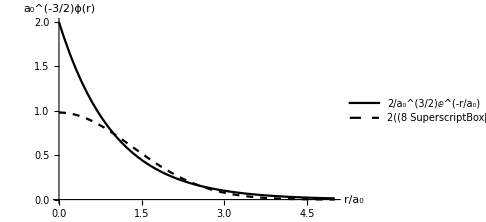

```mathematica
phi1s=(Integrate[Integrate[((1/(π*a^3))^(1/2)*ⅇ^(-r/a))^2 Sin[θ],{ϕ,0,2π}],{θ,0,π}])^(1/2);
phigauss=(Integrate[Integrate[(((2*(8/(9π*a^2)))/π)^(3/4)*ⅇ^(-(8/(9π*a^2))r^2))^2 Sin[θ],{ϕ,0,2π}],{θ,0,π}])^(1/2);

Plot[{phi1s/.a->1,phigauss/.a->1},{r,0,5},BaseStyle->{FontFamily->"Arial",FontSize->14},PlotStyle->{Directive[Black,PointSize[Large]],Directive[Black,Dashed,PointSize[Large]]},AxesStyle->Directive[Thick,Black],TicksStyle->Directive[Black, Thick],Ticks->Automatic,ImageSize->Medium, Exclusions->None,AxesOrigin->{0,0},AxesLabel->{"r/a_0","a_0^(-3/2)ϕ(r)"},PlotLegends->{"2/a_0^(3/2)ⅇ^(-r/a_0)","2((8 SuperscriptBox[α, 3])/π)^(1/4)ⅇ^(-αr^2)"}]
```

Figure 8.1 Plot of the radial component of the hydrogen 1s wavefunction (solid line) vs the Gaussian trial function optimized to yield the lowest energy (dashed line). The parameter α is given by α=8/(9π a_0^2).

#### Basis Functions Can Also Contain a Variational Parameter

To obtain an even better agreement between the variational calculation and the true energies and eigenstates, we could vary both the weights of our basis functions and a parameter within each of our basis functions. For example, instead of using hydrogen-like orbitals as our basis,

ϕ(r)=∑_n a_n ⅇ^(-Zr/a_0)

one could imagine that we could obtain a much better fit to wavefunctions of multielectron atoms if we allowed the effective nuclear charge ζ to vary as well as the weighting coefficients,

ϕ(r)=∑_n a_n ⅇ^(-ζ_nr/a_0)

Optimizing this sort of trial wavefunction is known as the nonlinear variational method. It is extremely time-intensive ( “expensive” in the language of computational chemistry) to perform this optimization because for each change in ζ_n, the matrices H and S must be recalculated. In practice, usually the ζ_n parameters are optimized based on a set of relevant atoms or molecules, and these optimized basis functions are then employed in a typical linear variational method calculation, where we vary only the coefficients  a_n. For example, when performing a calculation with the slater-type orbitals discussed earlier, one uses a set of basis functions with previously optimized values of ζ_n.

We’ll return to these ideas when we discuss computational chemistry later in the course.

### The Hartree-Fock Method with Orbitals as Linear Combination of Basis Functions

Keep in mind that each of our orbital functions ϕ_i is typically represented as a linear combination of basis functions,

ϕ_i(r_1)=∑_p C_pi f_p(r_1)

where C_pi is the weighting coefficient for each basis function f_p(r_1). That means that in the end, we are typically solving a matrix equation, just as we did for the more generic linear variational method. We won’t go through the details, but this equation takes the form

∑_p F_qp C_pi=ϵ_i∑_p S_qp C_pi

Or, in matrix form,

FC=SCϵ

This equation is similar to the one we saw for the variational method, where we can solve

S^-1 FC=Cϵ

for the eigenvector matrix C and the diagonal eigenvalue matrix ϵ. This equation is known as the Roothan equation. If you read the output from computational chemistry code, it may say something like “diagonalizing Fock matrix”, which means it is solving the Roothan equations for the eigenvectors and eigenvalues. This solution must be found iteratively through the SCF method.

### The Hartree-Fock Method Represents the Starting Point for Computational Chemistry

It must be said that Hartree-Fock calculations are rarely used in modern computational chemistry. That’s because they simply aren’t sufficiently accurate for most modern research. However, the Hartree-Fock method is still extremely important. It remains the starting point for almost every type of computational chemistry. For example, Møller–Plesset second-order perturbation theory is commonly used in computational chemistry, and it functions by finding the second-order perturbation corrections to the solutions from the Hartree-Fock Method. In addition, density functional theory, perhaps the most widely-used electronic structure method, bears a striking resemblance to the Hartree-Fock method, although the details are slightly different.

## Perturbation Theory

### Finding Solutions to an Unknown Problem by Small Changes to a Known Problem

The idea behind perturbation theory is that we can start with a problem that we do know how to solve and add new terms that give corrections, or perturbations, that account for the differences between the ideal and real systems. Let’s start again with the time-independent Schrödinger equation for some system,

Ĥ|ψ⟩=E|ψ⟩                                           Ĥ ψ=Eψ

If this unknown system resembles some well-characterized system that we have solved previously, we can write the Hamiltonian operator in the form

Ĥ=(Ĥ)^(0)+(Ĥ)^(1)

where (Ĥ)^(0)is the Hamiltonian operator for our known system that we can solve exactly,

(Ĥ)^(0)|ψ^(0)⟩=E^(0)|ψ^(0)⟩                                          (Ĥ)^(0)ψ^(0)=E^(0)ψ^(0)

The second term in the Hamiltonian represents the perturbation to the system.

### Example: The Anharmonic Oscillator

Remember that we already briefly discussed an example of such a perturbation in the context of the harmonic oscillator, where we represented the shape of our potential energy function as a Taylor series expansion about the minimum energy at r=r_0=0,

V(r)=1/2 kr^2+1/6 γr^3+1/24 δr^4+...

As we discussed previously, if we truncate at the third term in the expansion above (1/24 δr^4), we can write the TISE of the system as

(Ĥ)^(0)ψ(r)+(Ĥ)^(1)ψ(r)=E ψ(r)

Where

(Ĥ)^(0)=-ℏ^2/(2μ)d^2/dr^2+1/2 kr^2

Is the standard Hamiltonian for a harmonic oscillator, and the perturbation term

(Ĥ)^(1)=1/6 γr^3+1/24 δr^4

represents a correction for the anharmonicity of the potential. We can also write our wavefunction in the form of a perturbation to the known eigenfunctions of the unperturbed Hamiltonian,

ψ=ψ^(0)+ψ^(1)+ψ^(2)+...

where ψ^(0)represents the relevant energy eigenfunction of the harmonic oscillator. We can utilize the same representation for the energy of the system,

E=E^(0)+E^(1)+E^(2)+...

where E^(0)is the energy obtained from the unperturbed Hamiltonian for a harmonic oscillator operating on the unperturbed harmonic oscillator energy eigenfunction.

### Solving for the Perturbation Terms

We have now seen how we can conceptually set up the perturbation method, but the question now is how we solve for the perturbation terms in the energy and wavefunction. To do so, it is easiest to introduce the dimensionless parameter λ such that

( (Ĥ)^(0)+λ(Ĥ)^(1))ψ=E ψ

Then, we expand our eigenstate and energy as power series in λ,

E=(∑^N)_(i=0)λ^i E^(i)=E^(0)+λE^(1)+λ^2 E^(2)+...

ψ=∑_(i=0)^N λ^i ψ^(i)=ψ^(0)+λψ^(1)+λ^2 ψ^(2)+...

where N gives the number of terms that we are considering. In general, the terms become less important as i increases, so we usually truncate after some number of terms. We can then generally write the TISE as

( (Ĥ)^(0)+λ(Ĥ)^(1))(∑_(i=0) λ^i ψ^(i))=(∑_(i=0) λ^i E^(i))(∑_(i=0) λ^i ψ^(i))

Let’s take the case where N=1. Writing out all of the relevant terms in equation (155), we obtain

( (Ĥ)^(0)+λ(Ĥ)^(1))(ψ^(0)+λψ^(1))=(E^(0)+λE^(1))(ψ^(0)+λψ^(1))

Expanding this result gives

(Ĥ)^(0)ψ^(0)+λ (Ĥ)^(0)ψ^(1)+λ(Ĥ)^(1)ψ^(0)+λ^2(Ĥ)^(1)ψ^(1)=E^(0)ψ^(0)+λE^(0)ψ^(1)+λE^(1)ψ^(0)+λ^2 E^(1)ψ^(1)

If we collect the terms on each side by their order in λ, we obtain

(Ĥ)^(0)ψ^(0)+λ( (Ĥ)^(0)ψ^(1)+(Ĥ)^(1)ψ^(0))+λ^2(Ĥ)^(1)ψ^(1)=E^(0)ψ^(0)+λ(E^(0)ψ^(1)+E^(1)ψ^(0))+λ^2 E^(1)ψ^(1)

#### Zero-Order Terms

The first set of terms (black), known as the zero-order terms, simply give the TISE of the unperturbed system,

(Ĥ)^(0)ψ^(0)=E^(0)ψ^(0)

#### First-Order Terms

The second set of terms (blue), known as the first-order terms, give what is know as the first-order perturbation of the system,

(Ĥ)^(0)ψ^(1)+(Ĥ)^(1)ψ^(0)=E^(0)ψ^(1)+E^(1)ψ^(0)

Or, in bra-ket notation

(Ĥ)^(0)|ψ^(1)⟩+(Ĥ)^(1)|ψ^(0)⟩=E^(0)|ψ^(1)⟩+E^(1)|ψ^(0)⟩

We can obtain a more useful expression for the energies if we multiply both sides by the bra ⟨ψ^(0)|,

⟨ψ^(0)|(Ĥ)^(0)|ψ^(1)⟩+⟨ψ^(0)|(Ĥ)^(1)|ψ^(0)⟩=⟨ψ^(0)|E^(0)|ψ^(1)⟩+⟨ψ^(0)|E^(1)|ψ^(0)⟩

In bra-ket notation, an operator can act “backwards” onto a bra as well as forwards onto a ket, so we can write

⟨ψ^(0)|(Ĥ)^(0)=⟨ψ^(0)|E^(0)

E^(0)is just a constant, so it can be pulled in front of a bra, which gives us

E^(0)⟨ψ^(0)|ψ^(1)⟩+⟨ψ^(0)|(Ĥ)^(1)|ψ^(0)⟩=E^(0)⟨ψ^(0)|ψ^(1)⟩+⟨ψ^(0)|E^(1)|ψ^(0)⟩

Since the first term is the same on both sides, we obtain

⟨ψ^(0)|(Ĥ)^(1)|ψ^(0)⟩=⟨ψ^(0)|E^(1)|ψ^(0)⟩

=E^(1)⟨ψ^(0)|ψ^(0)⟩

Assuming our unperturbed eigenfunction is properly normalized, we have

⟨ψ^(0)|ψ^(0)⟩=1

Giving us

E^(1)=⟨ψ^(0)|(Ĥ)^(1)|ψ^(0)⟩

So we now have an expression for our first-order correction to the energy, E^(1). In a position-basis, we might write

E^(1)=∫ψ^((0)⋆)(Ĥ)^(1)ψ^(0)ⅆτ

If we truncate our perturbation at first order, then, we obtain

E=E^(0)+E^(1)

Obtaining the corresponding first-order wavefunctions ,

ψ=ψ^(0)+ψ^(1)

Is a bit more complicated, and we won’t go through the details at this moment.

#### Second-Order Terms

We also won’t go through the details of how the second-order terms are evaluated. Note that equation (158) doesn’t include all of the terms that are second-order in λ (meaning they contain a λ^2). For that, we would need another term in our expansions. The second-order terms are in fact included and utilized in many types of computation.

### Perturbation Theory and the Helium Atom

Let’s use perturbation theory to obtain an approximation of the ground-state energy of the helium atom. The starting point for our perturbation is similar to that for the variational method. We will again write the Hamiltonian in the form

Ĥ=(Ĥ)_H1+(Ĥ)_H2+e^2/(4 πϵ_0 r_(1,2))

our unperturbed eigenfunction ψ^(0) will be the product of the wavefunctions of two hydrogen-like atoms,

ψ^(0)=ψ_(1s)(r_1)ψ_(1s)(r_2)=ψ_(1s)(r_1,θ_1,ϕ_1)ψ_(1s)(r_2,θ_2,ϕ_2)

Using this formulation of the unperturbed wavefunction, we see that we can write our Hamiltonian as

Ĥ=(Ĥ)^(0)+(Ĥ)^(1)

where

(Ĥ)^(0)=(Ĥ)_H1+(Ĥ)_H2=-ℏ^2/(2 m_e)∇_1^2 -(2 e^2)/(4 πϵ_0)1/r_1+-ℏ^2/(2 m_e)∇_2^2 -(2 e^2)/(4 πϵ_0)1/r_2

and

(Ĥ)^(1)=e^2/(4 πϵ_0 r_(1,2))

Note that

(Ĥ)^(0)ψ^(0)=E^(0)ψ^(0)

That is, the unperturbed wavefunction ψ^(0)is an eigenfunction of the Hamiltonian with energy eigenvalue E^(0). We already have a formula for the first-order correction to the energy,

E^(1)=∫ψ^((0)⋆)(Ĥ)^(1)ψ^(0)ⅆτ

∫ ∫ψ_(1s)^⋆(r_1)ψ_(1s)^⋆(r_2)e^2/(4 πϵ_0 r_(1,2))ψ_(1s)(r_1)ψ_(1s)(r_2)ⅆ r_1ⅆ r_2

We won’t go through evaluating this integral, but we obtain

E^(1)=(5Z)/8((m_e e^4)/(16 π^2 ϵ_0 ℏ^2))

If we add this to E^(0),

E^(0)=-((Z^2 m_e e^4)/(32 π^2 ϵ_0 ℏ^2))-((Z^2 m_e e^4)/(32 π^2 ϵ_0 ℏ^2))

we obtain

E=E^(0)+E^(1)=(-Z^2/2-Z^2/2+(5Z)/8)((m_e e^4)/(16 π^2 ϵ_0 ℏ^2))

=(-Z^2+(5Z)/8)((m_e e^4)/(16 π^2 ϵ_0 ℏ^2))

For the helium atom, Z = 2, so we obtain −2.750 for our factor multiplying ((m_e e^4)/(16 π^2 ϵ_0 ℏ^2)), whereas we obtained −2.8477 using our effective nuclear charge method. The experimental result is −2.9033. If we used second-order perturbation theory, we could obtain −2.910, and higher-order perturbation would give us -2.9037.

### Limitations of Perturbation Theory

We have seen that perturbation theory can be a highly effective method to obtain an approximation to the true energy and eigenstate of a system. However, its accuracy is limited both by the number of terms included and by the accuracy of the underlying “unperturbed” system. If we start with a case that does not even remotely resemble the true wavefunction, it is unlikely that we will be able to obtain an accurate answer through any reasonable number of perturbation terms.